#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawignermix=Import["wigner_floquet0.dat"];
sp=Import["survivalprobability.dat"];
wg=Import["wignerresults.dat"];
```

```mathematica
(*Classical Hamiltonian*)
Δ=-2;
ϵ=8.0;
Kp=1;
ω=20;
ξ=0.25;
H[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2);
HD[q_,p_,t_]=-(Δ/2)*(q^2+p^2)+(Kp/4)*(q^2+p^2)^2-ϵ*(q^2-p^2)+ξ*(q^2+p^2)*Cos[ω*t];
```

```mathematica
H[0,0,0]
```

0.

```mathematica
(*Solving the Hamiltons equation*)
pin=0.0;
qin=0.01;
tf=20000;
T=2 Pi/ω;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
solt=NDSolve[{D[q[t],t]==D[HD[q[t],p[t],t],p[t]],D[p[t],t]==-D[HD[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
(*Classical trajectories and Poncaire sections*)
Tint=0.1;
T=2Pi/ω;
qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,Tint}];
qpt=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,T}];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
(*Wigner function and Poncaire sections*)
wigner2=Show[ListDensityPlot[datawignermix,PlotRange->{{-7,7},{-7,7},All},Frame->True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[0.5/0.35(#+0.35)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[qpt,PlotStyle->Darker[Green]]]
```

-Graphics-

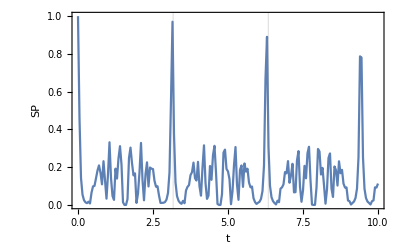

```mathematica
(*Survival probabilities*)
ListPlot[sp,PlotRange->All,Joined->True,Frame->True,GridLines->{{3.17,6.34},{}},FrameLabel->{"t","SP"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
wn=Table[{wg[[i,1]],wg[[i,3]]},{i,1,Length[wg]}];
```

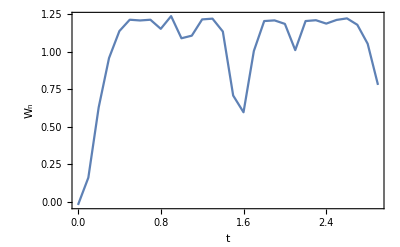

```mathematica
(*Negativities*)
ListPlot[wn,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","W_n"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
(2*π)/(-21.7226535+49.03617351)
```

0.230039

```mathematica
2*π/0.2300393836048665
```

27.3135